## If statement

```mathematica
f[x_]:=If[x>0,1,0]
```

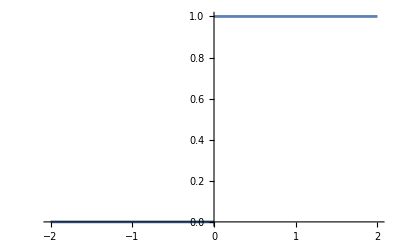

```mathematica
Plot[f[x], {x,-2,2}]
```

```mathematica
a=1;
If[a,"True","False","I don't know!"]
```

I don't know!

## Which statement

```mathematica
a=1;Which[a==1,"First",a==1,"Second",a<3,"Third"]
```

First

```mathematica
a=100;
Which[a==1,"First",a==1,"Second",a<3,"Third",True,"Other case"]
```

Other case

## Switch statement

```mathematica
what[a_]:=Switch[a,
_Integer,"An integer number",
_Real,"A real number",
_Complex, "A complex number",
_String,"A string",
_,"I can't do this, Dave!"
]
```

```mathematica
what[1]
```

An integer number

```mathematica
what[1.0]
```

A real number

```mathematica
what[what]
```

I can't do this, Dave!

```mathematica
Head[what]
```

Symbol

```mathematica
Head[1]
```

Integer

```mathematica
Head[1.0]
```

Real

```mathematica
Head["A"]
```

String